# Nanobody fits (L=144μm)

## Read data in

```mathematica
SetDirectory["/Users/hadjivz/Dropbox/Mac/Desktop/CodeOnline/Nanobody/L144/"];
files=FileNames["dat*.txt"];
files= files[[Ordering@PadRight@StringSplit[files,x:DigitCharacter..:>FromDigits@x]]];
dat=Table[Import[files[[f]],"Table"],{f,1,Length[files]}]//N;
```

## Define model and fit simultaneously

From A, B, p to ks functions

```mathematica
fko := Function[{p,B, A}, p - p^2 B / (p B + A)]
fkN := Function[{p,B, A},(p B + A)]
fkr := Function[{p,B, A},p^2 B / (p B + A)]
```

Format data for simultaneous fit

```mathematica
datIndexed = Table[Table[{dat[[i,j,1]], i, dat[[i,j,2]]}, {j,1,Length[dat[[i]]]}], {i,1,Length[dat]}];
```

```mathematica
(*fitted initial intensity point (at t=0) cannot be higher than first measurement at t0>0*)
ciMax=Table[dat[[i,1,2]], {i,1,Length[dat]}];
```

Sample length up to t=4500s across experiments

```mathematica
maxT = 4500;
dat1=Table[Table[If[dat[[j,i,1]]<maxT, dat[[j,i]]], {i, 1, Length[dat[[j]]]}], {j,1,Length[dat]}];
dat2=Table[DeleteCases[dat1[[j]], Null], {j,1,Length[dat1]}];
datIndexed = Table[Table[{dat2[[i,j,1]], i, dat2[[i,j,2]]}, {j,1,Length[dat2[[i]]]}], {i,1,Length[dat2]}];
```

Fits (simultaneous)

```mathematica
modelc1:=c1(1+A t+B(1-Exp[-p t]));
modelc2:=c2(1+A t+B(1-Exp[-p t]));
modelc3:=c3(1+A t+B(1-Exp[-p t]));
modelc4:=c4(1+A t+B(1-Exp[-p t]));
modelc5:=c5(1+A t+B(1-Exp[-p t]));
modelc6:=c6(1+A t+B(1-Exp[-p t]));
modelc7:=c7(1+A t+B(1-Exp[-p t]));
modelc8:=c8(1+A t+B(1-Exp[-p t]));
modelc9:=c9(1+A t+B(1-Exp[-p t]));
modelc10:=c10(1+A t+B(1-Exp[-p t]));
modelc11:=c11(1+A t+B(1-Exp[-p t]));
modelc12:=c12(1+A t+B(1-Exp[-p t]));
modelc13:=c13(1+A t+B(1-Exp[-p t]));

modelSimultaneous[index_]:=KroneckerDelta[index-1]*modelc1+KroneckerDelta[index-2]*modelc2+KroneckerDelta[index-3]*modelc3+KroneckerDelta[index-4]*modelc4+KroneckerDelta[index-5]*modelc5+KroneckerDelta[index-6]*modelc6+KroneckerDelta[index-7]*modelc7+KroneckerDelta[index-8]*modelc8+KroneckerDelta[index-9]*modelc9+KroneckerDelta[index-10]*modelc10+KroneckerDelta[index-11]*modelc11+KroneckerDelta[index-12]*modelc12+KroneckerDelta[index-13]*modelc13;
```

```mathematica
ciStart = 0.1;
fitsSimultaneous=NonlinearModelFit[Flatten[datIndexed,1],{modelSimultaneous[indexi],A>0, B>0 , 0.1>p>0,
 ciMax[[1]]>c1>0,
 ciMax[[2]]>c2>0,
 ciMax[[3]]>c3>0,
 ciMax[[4]]>c4>0,
 ciMax[[5]]>c5>0,
 ciMax[[6]]>c6>0,
 ciMax[[7]]>c7>0,
 ciMax[[8]]>c8>0,
 ciMax[[9]]>c9>0,
ciMax[[10]]>c10>0,
 ciMax[[11]]>c11>0,
 ciMax[[12]]>c12>0,
 ciMax[[13]]>c13>0
},{{c1,ciStart},{c2,ciStart},{c3,ciStart},{c4,ciStart},{c5,ciStart},{c6,ciStart},{c7,ciStart},{c8,ciStart},{c9,ciStart},{c10,ciStart},{c11,ciStart},{c12,ciStart},{c13,ciStart},{A, 0.1}, {B,30}, {p,0.01}},{t,indexi},VarianceEstimatorFunction->(Mean[Abs[#]]&)];
```

Translate (A, B, p) from fit to (ko, kN, kr) and plot fitted curves with experimental data

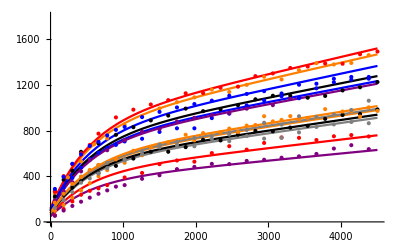

```mathematica
imin=1;
imax=13;
maxt = maxT;
maxy=1800;
imin=1;
imax=13;
Show[Plot[Evaluate@Table[modelSimultaneous[i]/.fitsSimultaneous["BestFitParameters"],{i,imin,imax}],{t,0,maxt},PlotStyle->{Orange, Red, Purple, Blue, Black, Gray},PlotRange->{{0,6000},{0,maxy}}],
ListPlot[Table[dat[[i]], {i,imin,imax}],PlotStyle->{Orange, Red, Purple, Blue, Black, Gray}],TicksStyle->Directive[Black, 14], PlotRange->{{0,maxT},{0,maxy}}]
```

```mathematica
ko=fko[p,B,A]/.fitsSimultaneous["BestFitParameters"]
kN=fkN[p,B,A]/.fitsSimultaneous["BestFitParameters"]
kr=fkr[p,B,A]/.fitsSimultaneous["BestFitParameters"]
```

0.000184971

0.0130028

0.00172095

```mathematica
fitsSimultaneous["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
c1 | 76.3325 | 1.53813 | 49.6267 | 2.65854×10^-134
c2 | 59.1096 | 1.194 | 49.5055 | 4.71693×10^-134
c3 | 49.1121 | 0.995076 | 49.3551 | 9.6183×10^-134
c4 | 96.0915 | 1.93463 | 49.6693 | 2.17421×10^-134
c5 | 99.5377 | 2.0007 | 49.7514 | 1.47573×10^-134
c6 | 71.044 | 1.43238 | 49.5986 | 3.03639×10^-134
c7 | 114.343 | 2.29928 | 49.7297 | 1.63497×10^-134
c8 | 118.435 | 2.37987 | 49.7653 | 1.38203×10^-134
c9 | 94.326 | 1.89553 | 49.7623 | 1.40174×10^-134
c10 | 106.446 | 2.1422 | 49.6901 | 1.97117×10^-134
c11 | 73.1896 | 1.47403 | 49.6527 | 2.3516×10^-134
c12 | 77.1786 | 1.55506 | 49.6307 | 2.60908×10^-134
c13 | 79.0485 | 1.59164 | 49.665 | 2.21919×10^-134
A | 0.00126193 | 0.0000290051 | 43.5071 | 4.41698×10^-121
B | 6.16019 | 0.135649 | 45.4126 | 2.40096×10^-125
p | 0.00190592 | 0.0000180667 | 105.494 | 8.1744×10^-215

Calculate s.e.m. for ko, kN, kr

```mathematica
(*variance for A, B, p from fits above*)
LOP144={varp -> (0.00001806668885367165)^2, varA -> (0.000029005101616072976)^2, varB ->(0.13564939108979743)^2, p->0.0019059242336493607,A->0.0012619287187095227, B->6.160190515040564};
ParsNow=LOP144;

(*Error propagation formula for kN*)
VarkN = varp varB + varp B^2 + varB p^2 + varA;
fskN=(D[(A+B p),A]^2 varA + D[(A+B p),B]^2 varB +  D[(A+B p),p]^2 varp );
semkn=Sqrt[fskN/.ParsNow]
```

0.000282965

```mathematica
(*Error propagation formula for kr*)
fskr=(D[p^2 B/(p B + A),A]^2 varA + D[p^2 B/(p B + A),B]^2 varB +  D[p^2 B/(p B + A),p]^2 varp );
semkr=Sqrt[fskr/.ParsNow]
```

0.0000186695

```mathematica
(*Error propagation formula for ko*)
Varko = varp + varkr;
semko=Sqrt[Varko/.{varkr->fskr}/.ParsNow]
```

0.0000259799